# Movie Recommendation using Mathematica

```mathematica
Quit[]
```

We shall first set the working directory the same as this notebook, necessary to import the data successfully

```mathematica
SetDirectory[NotebookDirectory[]]
```

Importing data

```mathematica
data = SemanticImport["data.csv"];
```

The data is imported as a dataset object

```mathematica
Head@data
```

Dataset

Structure of the dataset:

```mathematica
data[RandomInteger[Length[data]]]
```

```mathematica
Dimensions[data]
```

{1048335,4}

CID: customer ID
Rating: Rating given by the user for that movie
Date : Date the rating was given . In the DD-MM-YYYY format
MovieID: unique  Id assigned to each movie

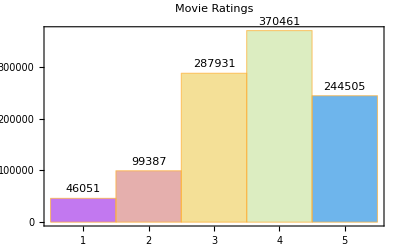

```mathematica
Histogram[data[All,"Rating"],LabelingFunction->Above,PerformanceGoal->"Speed",PlotTheme->"Web",PlotLabel->"Movie Ratings",ChartStyle->"Pastel"]
```

We observe that the ratings tend to be relatively positive (>3).
One reason for this might be that unhappy/unsatisfied customers tend to leave without making the effort of rating an experience they did not enjoy.

The number of ratings for each movie is not uniform . There is a huge difference in the number of observations for each movie.

```mathematica
temp =Counts[data[All,"MovieID"]];
```

We order the data in descending order to make this difference visible. Printing the 10 most popular movies according to the number of ratings

```mathematica
Reverse[Sort[temp]][1;;10]
```

```mathematica
PieChart[temp,ChartStyle->"Pastel",ChartLabels->Placed[Range[241],"RadialOutside"],PerformanceGoal->"Quality"]
```

-Graphics-

Creating a function to split the dataset on a proportion given by the user
Parameters: 
dataset,
percentage of dataset to be assigned to the training set,
percentage of dataset to be assigned to validation set

```mathematica
Remove[split,test,train,val];
```

```mathematica
split[data_,prop1_,prop2_:0]:=
Module[{temp,n1,n2,r1,r2},
temp = RandomSample[data];
n1= Round[Length[data]*prop1/100];
r1 = Range[1,n1];
train = temp[r1];
If[prop2 !=0,
n2 = Round[Length[data]*prop2/100];
n2 = n2+n1;
r2 = Range[n1+1,n2];
val = temp[r2];
test = temp[n2+1;;];
,
test = temp[n1+1;;];
]]/;prop1>0&&prop2>=0&&prop1+prop2<100
```

How the function works:
The user inputs the desired percentage split of the data
It is optional if you want to create a validation set, if yes then a second percentage is to be inputted
Percentages entered can not be equal or greater than 100 since the test set will be calculated using the remaining dataset
Percentages can’t be negative for obvious reasons

```mathematica
Clear[train,test,val];
split[data,70,15];
```

```mathematica
List[Dimensions[train],Dimensions[val],Dimensions[test]]
```

{{733834,4},{157250,4},{157251,4}}

Extracting columns from training dataset

```mathematica
cid = Normal[train[[All,"CID"]]];
```

```mathematica
movieID = Normal[train[[All,"MovieID"]]];
```

```mathematica
rating = Normal[train[[All,"Rating"]]];
```

We shall first try the naive method of simply predicting the average for everything

```mathematica
pred = ConstantArray[Round[Mean[rating]],Length[val]];
```

Creating function to return Residual Mean Squared Error

```mathematica
RMSE[obs_,pred_]:=Return[N@Sqrt[Mean[Power[obs-pred,2]]]]
```

```mathematica
RMSE[Normal[val[[All,"Rating"]]],pred]
```

1.13456

What if we just randomly predict a rating, no reasoning at all, simply a random pick between 1-5

```mathematica
pred = RandomChoice[Range[5],Length[val]];
```

```mathematica
RMSE[Normal[val[[All,"Rating"]]],pred]
```

1.88619

As expected , this is not a viable method of predicting

### Linear Regression

```mathematica
combinedList = Transpose[{cid,movieID,rating}];
```

Fitting a linear regression with target variable as rating

```mathematica
fit1 = LinearModelFit[Transpose[{cid,rating}],x,x]
```

FittedModel[3.63969-1.47836×10^-9 x]

The best fit achieved is given by:

```mathematica
fit1["BestFit"]
```

3.63969-1.47836×10^-9 x

Predict using the linear model

```mathematica
pred = Map[fit1,Normal[val[[All,"CID"]]]];
```

```mathematica
RMSE[Normal[val[[All,"Rating"]]],pred]
```

1.07447

We see a significant improvement in the RMSE.

### Using Predict

Predict is a versatile function in Mathematica that allows us to fit various methods on our dataset simultaneously . Here I use predict to train a model to predict the Ratings by taking every other column as a variable

```mathematica
p = Predict[train->"Rating"]
```

PredictorFunction[…]

The method chosen is : GradientBoostedTrees
Further Information on the training process is given below

```mathematica
Information[p]
```

Predictor information
Data type | {Numerical,Text,Numerical}
Standard deviation | 1.01 ± 0.0026
Method | GradientBoostedTrees
Single evaluation time | 9.05 ms/example
Batch evaluation speed | 8.62 examples/ms
Loss | 1.46 ± 0.0027
Model memory | 687. kB
Training examples used | 733834 examples
Training time | 2 42
 |

Predicting Ratings using the model ‘p’ on the validation set.

```mathematica
pred = p[val[All,{"CID","Date","MovieID"}]];
```

```mathematica
RMSE[Normal[val[[All,"Rating"]]],pred]
```

1.01106

We achieve the lowest RMSE yet thus we can move forward with predicting on the test-set

```mathematica
pred = p[test[All,{"CID","Date","MovieID"}]];
```

```mathematica
RMSE[Normal[test[[All,"Rating"]]],pred]
```

1.01006

An acceptable performance is achieved on the test set

### Correlation based Recommendation

In this section i aim to recommend movie titles to someone based on their previously rated movies

Taking a random subset of 10,000 rows from the dataset

```mathematica
randomsubset = RandomSample[data][[1;;10000]];
```

Importing the DataReshape package to pivot the dataset such that each column represents a movie, each row represents a customer and the values are the ratings present in our data

```mathematica
Import["https://raw.githubusercontent.com/antononcube/MathematicaForPrediction/master/DataReshape.m"]
```

Pivoting the data

```mathematica
movieRating = ToWideForm[randomsubset,"CID","MovieID","Rating"];
```

This will result in a massively sparse matrix since not all customers have watched all movies or have not rated everything they watched
The following is the row representing customer with CID  2449213 . We see that this customer has rated the movie with movieID 191. Most of the ratings are missing since this user did not rate/watch them.

```mathematica
movieRating[1]
```

One might ask how many values are missing from this dataset

We have the following number of elements in our dataset:

```mathematica
sizemovieRating = Dimensions[movieRating][[1]]*Dimensions[movieRating][[2]]
```

2171904

We only have Ratings for the number of observations in the validation dataset

```mathematica
sizeRating = Dimensions[randomsubset][[1]]
```

10000

Percentage of data missing:

```mathematica
N[(sizemovieRating-sizeRating)*100/sizemovieRating]
```

99.5396

It would not be far fetched to say that we barely have any data in this situation

For this demonstration we use 400 observations of the dataset

```mathematica
experimentData = randomsubset[1;;400];
```

Pivoting the dataset into a sparse matrix

```mathematica
expRatingdata = ToWideForm[experimentData,"CID","MovieID","Rating"];
```

```mathematica
expRatingdata
```

Dataset[<>]

Dimensions of the dataset

```mathematica
Dimensions[expRatingdata]
```

{400,78}

MovieIDs which are included in this set of observations

```mathematica
moviesInExp = expRatingdata[[1,Keys]][2;;]//Normal
```

{191,241,45,26,171,223,143,97,197,208,111,89,199,148,175,46,181,30,44,132,159,8,28,18,39,52,78,118,108,187,152,33,76,58,215,83,166,47,79,74,77,239,25,161,90,209,240,160,133,138,185,127,225,129,156,188,167,107,131,50,88,201,24,3,224,202,189,16,49,168,216,73,68,227,17,232,57}

Initializing an empty matrix

```mathematica
expdatamatrix={}
```

{}

Reshaping the matrix into an appropriate size

```mathematica
expdatamatrix = ArrayReshape[expdatamatrix,{Length[moviesInExp],Dimensions[expRatingdata][[1]]}];
```

Filling up the matrix with ratings for each movie as columns of the matrix

```mathematica
For[i=2,i<Length[moviesInExp]+2,i++,
expdatamatrix[[i-1]]=Normal[expRatingdata[All,i]]]
```

Replacing all missing values by 0 since it’s impossible to have a 0 rating in our data

```mathematica
expdatamatrix = expdatamatrix/.Missing[]->0;
```

FInding the Correlation between the different movies [columns of the matrix]. We are trying to find similar movies based in the rating pattern of users

```mathematica
cor = Correlation[Transpose[expdatamatrix]];
```

Creating a list of movieIDs according to the most correlated movies to the 1st movie in our dataset as a demonstration

```mathematica
movielist = moviesInExp[[Reverse@Ordering@cor[[1]]]]
```

{199,111,33,58,78,209,52,181,89,171,133,79,26,197,30,187,148,241,77,108,138,46,8,118,239,223,28,17,57,232,227,68,73,216,168,49,16,189,202,224,3,24,201,88,50,131,167,188,129,225,127,185,160,90,25,74,47,39,18,159,44,208,97,107,161,132,215,166,175,156,83,240,76,45,143,152,191}

Confirming that our movieIDs have indeed been ordered appropriately

This order of movies would yield a biased result since there are many movies who will have just one rating. This method of correlation tends to give more weight to these rather than similar movies

```mathematica
moviesInExp
```

{191,241,45,26,171,223,143,97,197,208,111,89,199,148,175,46,181,30,44,132,159,8,28,18,39,52,78,118,108,187,152,33,76,58,215,83,166,47,79,74,77,239,25,161,90,209,240,160,133,138,185,127,225,129,156,188,167,107,131,50,88,201,24,3,224,202,189,16,49,168,216,73,68,227,17,232,57}

Creating a constant array of the size of number of movies in the dataset

```mathematica
movieOrder =ConstantArray[0,Length[moviesInExp]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Length[moviesInExp]
```

77

Filling the elements with the number of missing ratings for the movies, now replaced by 0

```mathematica
For[i=1,i<Length[moviesInExp]+1,i++,
movieOrder[[i]]=Count[expdatamatrix[[i]],0]]
```

Number of observations we did not have ratings for for each movie

```mathematica
movieOrder
```

{362,382,398,396,397,392,381,399,367,399,383,398,389,391,357,397,398,364,399,398,399,395,383,399,399,398,397,395,394,391,393,397,398,390,395,396,395,399,397,399,394,398,399,398,399,398,398,399,397,397,399,399,399,399,395,399,399,398,399,399,399,399,399,399,399,399,399,399,399,399,399,399,399,399,398,399,399}

Ordering the list of movies accordingly

```mathematica
movieorder = movielist[[Ordering@movieOrder]]
```

{30,199,241,89,52,111,133,8,26,216,197,232,209,227,57,3,46,17,168,16,25,58,49,78,187,28,68,202,129,225,33,79,148,108,223,73,24,88,131,167,39,143,181,171,77,138,118,239,189,224,201,50,188,127,185,160,90,74,47,18,159,44,208,97,107,161,132,215,166,175,156,83,240,76,45,152,191}

Importing dataset containing movie titles

```mathematica
movieNames = SemanticImport["movie_titles.csv"];
```

Structure of the dataset

```mathematica
movieNames//First
```

Converting the ordered lists of movies into a dataset

```mathematica
tempDataset=AssociationThread[ToString/@{MovieID}->#]&/@movielist[[Ordering@movieOrder]];
tempDataset = Dataset@tempDataset;
```

Joining the two datasets based on movieID

```mathematica
bestRecommendations = Dataset[JoinAcross[tempDataset,movieNames,Key["MovieID"]]];
```

Initializing array to hold titles for corresponding IDs with dummy values

```mathematica
titles = ConstantArray["MovieTitle",Length[movieorder]];
```

How many Distinct movies were present in the dataset

```mathematica
Length[movieorder]
```

77

Filling the array with movie titles corresponding to their movie ID

```mathematica
For[i=1,i<37,i++,
titles[[i]]= bestRecommendations[SelectFirst[#MovieID === movieorder[[i]]&],"Title"]]
```

Displaying the movie for which we are trying to find similar movies

```mathematica
bestRecommendations[SelectFirst[#MovieID === moviesInExp[[1]]&],"Title"]
```

X2: X-Men United

Allowing the user to decide how many of the most similar movies they want to see

```mathematica
Manipulate[titles[[Range[n]]],{n,1,Length[titles]-1,1}]
```

As expected , we see movies  which share genres are much more similar than those that have vastly different genres.